### Test with sech^2 potential

```mathematica
V[x_,p_]:=1/Cosh[x]^2;
params = Association["a"->-10, "b"->10,"n"->1000,"m"->100,"kmin"->0.01,"kmax"->2.001,"numk"->100, "TCalcStep"->50];
params["h"]=(params["b"]-params["a"])/params["n"];
kgrid = kGrid[params];
```

```mathematica
d2mat = D2Matrix[params];
emat=EMatrixKVec[kgrid,params];
yyvec=yvecKVec[kgrid,params];
```

```mathematica
psiSol=SchrEqOfV[V,0,params,kgrid,d2mat,emat,yyvec];
```

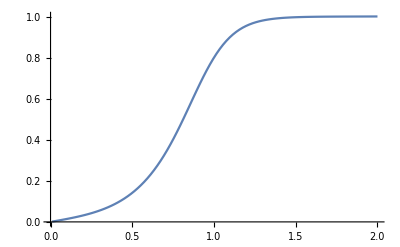

```mathematica
ListPlot[Abs[TofVVec[V,0,params,kgrid,d2mat,emat,yyvec]], Joined->True]
```